```mathematica
SetDirectory["/Users/tom/Desktop/CLASSES/VirtualQabs/phys340/e_over_m"]
```

/Users/tom/Desktop/CLASSES/VirtualQabs/phys340/e_over_m

```mathematica
d = Import["2000V-0.5A-down.txt","tsv"]
```

{{9.229,2.6008},{9.0764,2.6167},{8.8124,2.6335},{8.5428,2.6672},{8.3181,2.6953},{8.0597,2.7234},{7.8182,2.7571},{7.5373,2.8077},{7.1947,2.8526},{6.9194,2.8975},{6.6667,2.9312},{6.3352,3.0155},{5.9926,3.066},{5.6724,3.1335},{5.223,3.2458},{4.8018,3.3244},{4.4366,3.4312},{4.1389,3.5154},{3.7738,3.5997},{3.3638,3.7513},{3.0099,3.8524},{2.7178,3.9311},{2.538,4.0041},{2.2291,4.0828},{1.937,4.1839},{1.6898,4.2625},{1.3977,4.3692},{1.1731,4.4647},{0.9259,4.5321},{0.6956,4.6389}}

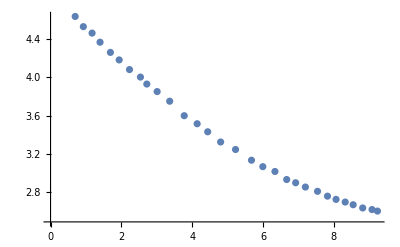

```mathematica
ListPlot[d]
```

```mathematica
f=FindFit[d,y0-Sqrt[r^2-(x-x0)^2],{y0,{r,10},x0},x]
```

{y0→34.1235,r→31.6795,x0→12.2896}

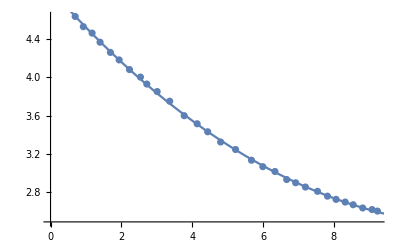

```mathematica
Show[{ListPlot[d],Plot[y0-Sqrt[r^2-(x-x0)^2]/.f,{x,0,10}]}]
```

```mathematica
i=0.5
mu = 4 Pi* 10^-7
Nt =124
Dia = .21
V=2000
r=.316
B=16 mu Nt i /(Sqrt[125] Dia)
em = 2 V /(B^2 r^2)
em0 = 1.75 10^11
(em-em0)/em0* 100
```

0.5

π/2500000

124

0.21

2000

0.316

0.000530942

1.42099×10^11

1.75×10^11

-18.8005